## Weak Lensing Checks

## Test and Plot WL Quantities

```mathematica
powerSpectrum[0.01,100]
```

0.0784715

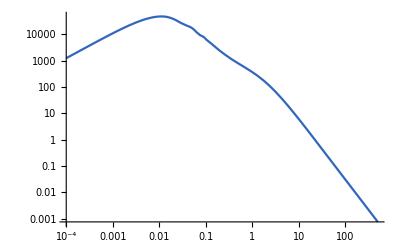

```mathematica
LogLogPlot[{powerSpectrum[0.5, kkk]}, {kkk,0.0001,500}, PlotLegends->Automatic, PlotRange->Automatic]
```

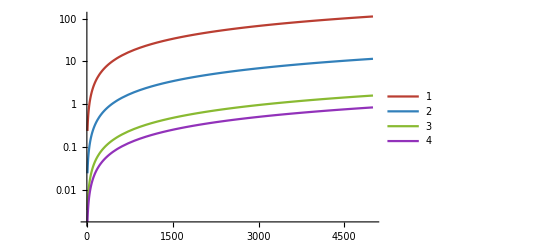

```mathematica
LogPlot[{ kofell[0.01,ell],kofell[0.1,ell], kofell[0.9,ell], kofell[2.5,ell]}, {ell,10,5000}, PlotLegends->Automatic, PlotRange->Automatic]
```

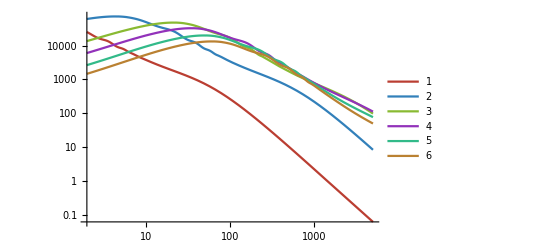

```mathematica
LogLogPlot[Evaluate@(pLimber[#, eee]&/@{0.01,0.1,0.5,0.9,1.5,2.1}), {eee,2,5000}, PlotLegends->Automatic, PlotRange->All]
```

```mathematica
$zbinsEquiPopu
```

{0.001,0.417121,0.558605,0.675825,0.785857,0.896692,1.01497,1.1494,1.31638,1.56301,2.5}

```mathematica
LogLinearPlot[{Evaluate@(lensKernelGG[zz, #,# ]&/@Range[1,10])}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotRange->All]
```

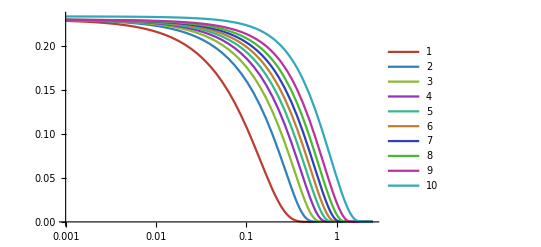

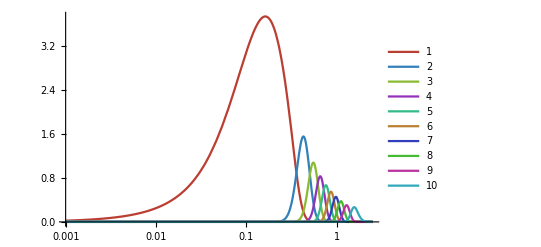

```mathematica
LogLinearPlot[{Evaluate@(lensKernelGI[zz, #,# ]&/@Range[1,10])}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotRange->All]
```

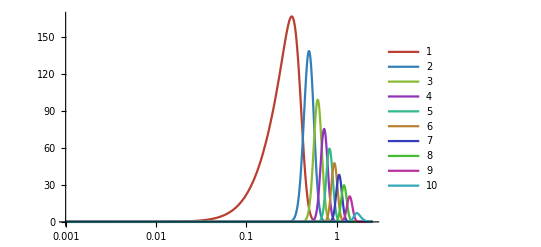

```mathematica
LogLinearPlot[{Evaluate@(lensKernelII[zz, #,# ]&/@Range[1,10])}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotRange->All]
```

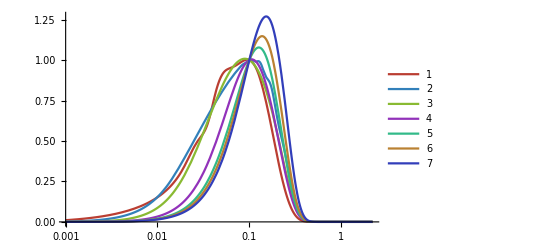

```mathematica
LogLinearPlot[Evaluate@((pijIntegrandGGInterpolFunc[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]
```

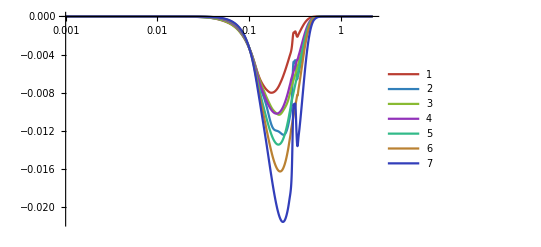

```mathematica
LogLinearPlot[Evaluate@((pijIntegrandGIInterpolFunc[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]
```

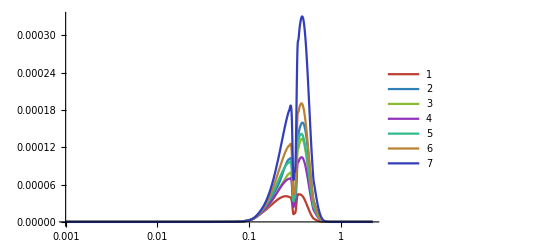

```mathematica
LogLinearPlot[Evaluate@((pijIntegrandIIInterpolFunc[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]
```

```mathematica
(*LogLinearPlot[Evaluate@((WeakLensingFisherTools`DIAInterpol[zzz, #, 1,1]/Max[pijIntegrandGGInterpolFunc[0.1, #, 1,1 ]])&/@{10,100,200,500,1000,1500,3500}), {zzz,0.001,2.2}, PlotLegends->Automatic, PlotRange->All]*)
```

```mathematica
CijGG[150,2,2, shearshearIntegrand->pijIntegrandGGInterpolFunc]//AbsoluteTiming
```

{0.216932,1.33827×10^-9}

```mathematica
CijGG[150,2,2, shearshearIntegrand->pijIntegrandGG]//AbsoluteTiming
```

{0.537603,1.33827×10^-9}

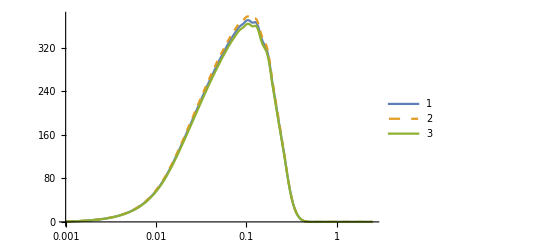

```mathematica
LogLinearPlot[{ pijIntegrandGGInterpolFunc[zz, 100, 1,1 ], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[Omegam, $epsilonstep]], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[Omegam, -$epsilonstep]]}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotStyle->{Thick, Dashed, Thick, DotDashed}]
```

```mathematica
$paramoptions
```

{Omegam→0.32,Omegab→0.05,hubble→0.67,ns→0.96,sigma8→0.815584,$aIA→1.72,$eIA→-0.41,$bIA→2.17}

```mathematica
LogLinearPlot[{ pijIntegrandGGInterpolFunc[zz, 100, 1,1 ], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[Omegam, $epsilonstep]], pijIntegrandGGInterpolFunc[zz, 100, 1,1 , epsilonChangeParameter[Omegam, -$epsilonstep]]}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotStyle->{Thick, Dashed, Thick, DotDashed}]
```

-Graphics-

```mathematica
ello=1000;
```

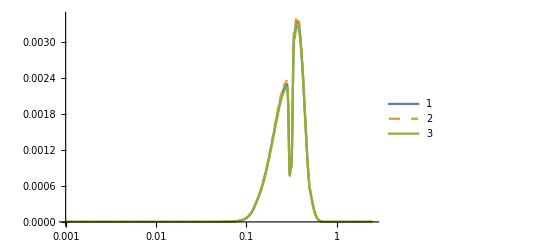

```mathematica
LogLinearPlot[{ pijIntegrandIIInterpolFunc[zz, ello, 1,1 ], pijIntegrandIIInterpolFunc[zz, ello, 1,1 , epsilonChangeParameter[Omegam, $epsilonstep]], pijIntegrandIIInterpolFunc[zz, ello, 1,1 , epsilonChangeParameter[Omegam, -$epsilonstep]]}, {zz,0.001,2.5}, PlotLegends->Automatic, PlotStyle->{Thick, Dashed, Thick, DotDashed}, PlotRange->All]
```

```mathematica
WeakLensingFisherTools`Private`DIAInterpol[100]
```

InterpolatingFunction[…]

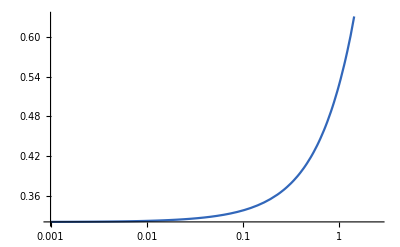

```mathematica
LogLinearPlot[0.32/Growth[zz,kofell[zz,1000]], {zz,0.001,2.5}]
```

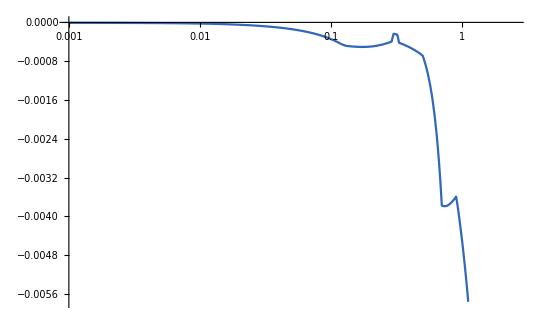

```mathematica
LogLinearPlot[curlyFIA[zz], {zz,0.001,2.5}]
```

```mathematica
cijStd=Table[{lll,CijGG[lll,2,1, shearshearIntegrand->pijIntegrandGG]}, {lll,$ellbinscenters}];
```

```mathematica
cijInt=Table[{lll,CijGG[lll,2,1, shearshearIntegrand->pijIntegrandGGInterpolFunc]}, {lll,$ellbinscenters}];
```

```mathematica
cijAllInt=Table[{lll,Cij[lll,2,1, shearshearIntegrand->pijIntegrandGGInterpolFunc]}, {lll,$ellbinscenters}];
```

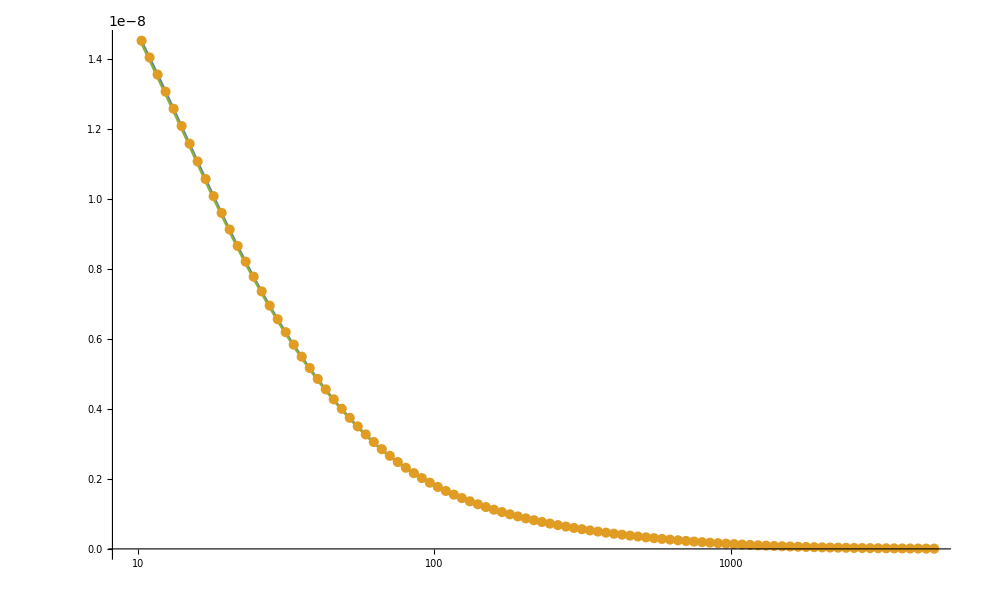

```mathematica
ListLogLinearPlot[{cijStd, cijInt, cijAllInt}, Joined->{True,False}]
```

```mathematica
Dynamic[{Global`proga, Global`progb, Global`progell}]
```

```mathematica
FisherWLSimple[1,1]
```